```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mcmcclur/GitHubDocuments/MarksMath/writ/MapProjection/newerFigures

```mathematica
landData = Import["ne_110m_land-geo.json"];
parallels=Line[Table[Table[{lng,lat},{lng,-180,180,5}],{lat,-85,85,10}]];
meridians=Line[Table[Table[{lng,lat},{lat,-85,85,5}],{lng,-180,180,10}]];
land = Map[Polygon["coordinates" /. #]&, "geometry" /. ("features" /. landData)];
```

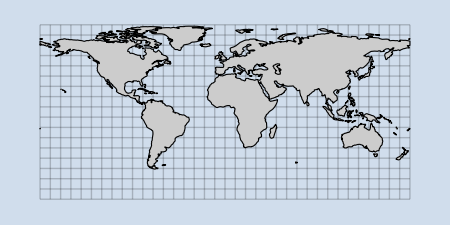

```mathematica
im = Graphics[{{Opacity[0.2],parallels,meridians}, {GrayLevel[0.8],EdgeForm[Black],land}}, ImageSize -> 450,Background->Lighter[ColorData["Aquamarine"][1],0.5], PlotRange -> {{-179,179},{-90,90}}]
```

```mathematica
globe = ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]} ,
{u,0,2Pi},{v, 0,Pi}, Mesh->None,PlotPoints->100,
TextureCoordinateFunction->({#4,1-#5}&), Boxed->False,
PlotStyle->Texture[Show[im,ImageSize->1000]],
Axes->False,RotationAction->"Clip",
ViewPoint -> {-2.026774,2.07922,1.73753418},
ImageSize->500]
```

-Graphics3D-

```mathematica
fig1 = Rasterize[Overlay[{
Grid[{{globe,mPic}},Spacings->4],
Graphics[{Arrow[{{-3,0},{0.5,0}}]}, PlotRange -> 10]},
Alignment->Center], 
RasterSize->1000,ImageSize->500]
```

-Graphics-

```mathematica
addZero[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{(x2*y1-x1*y2)/(y1-y2),0},{x2,y2}}/;y1*y2<0;
addZero[pair:{{x1_,y1_},{x2_,y2_}}]:=pair/;y1*y2≥0;
addZeros[list:{{_?NumericQ,_?NumericQ}..}]:=Flatten[Drop[#,-1]&/@(addZero/@Partition[Append[list,First[list]],2,1]),1];
cmpNorth=DeleteCases[{land/.Polygon[vv_]:>Polygon[addZeros/@vv],meridians,parallels},{x_?NumericQ,y_?(NumericQ[#]&&#<0&)},Infinity];
cmp={{Opacity[0.4],meridians,parallels},land};
```

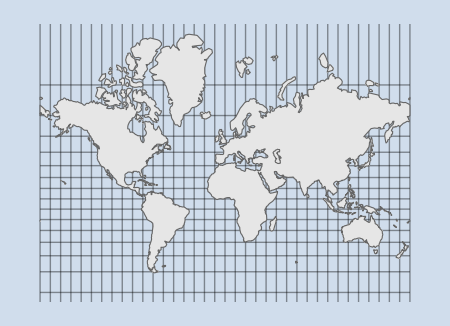

```mathematica
showProj[T_,north_:False] := Module[
{P,P1},
P1[{lng_?NumericQ,lat_?NumericQ}]:=T[{lat,lng}];
P[{lng_?NumericQ,lat_?NumericQ}]:=P1[N[{lng*Degree,lat*Degree}]]/Degree;
P[list_List]:=P/@list;
P[Line[points_]]:=Line[P[points]];
P[Polygon[points_]]:={GrayLevel[0.9],EdgeForm[GrayLevel[0.4]],Polygon[P[points]]};
P[x_]:=x;
Graphics[P[cmp],
Background->Lighter[ColorData["Aquamarine"][1],0.5]]]
mPic = Show[showProj[{#[[2]],Log[Abs[Tan[#[[1]]]+Sec[#[[1]]]]]}&], 
ImageSize->450, Axes -> False,PlotRange -> {{-179,179},{-90,170}}]
```

```mathematica
Export["Figure1.png", fig1]
```

Figure1.png

```mathematica
parallels=Line[Table[Table[{lng,lat},{lng,-180,180,5}],{lat,-85,85,10}]];
meridians=Line[Table[Table[{lng,lat},{lat,5,65,5}],{lng,-170,170,10}]];
```

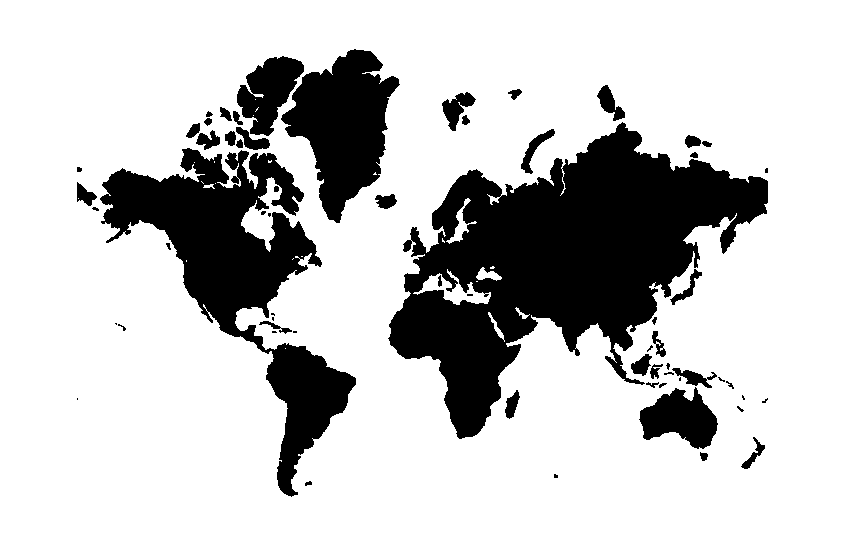

```mathematica
Graphics[Cases[im, 
Polygon[pts_] :> Polygon[Map[{#[[1]], Log[Abs[Sec[#[[2]]*Degree]+Tan[#[[2]]*Degree]]]/Degree}&, pts,{2}]]
, Infinity]]
```

```mathematica
Degree//N
```

0.0174533

```mathematica
M = {
{1,2,-3},
{0,-4,5},
{0,0,6}
};
Eigensystem[M]
```

{{6,-4,1},{{-4,5,10},{-2,5,0},{1,0,0}}}

```mathematica
M = {
{2,3,-4},
{0,-5,6},
{0,0,7}
};
Eigensystem[M]
```

{{7,-5,2},{{-1,1,2},{-3,7,0},{1,0,0}}}

```mathematica
M = {
{2,3,-5},
{0,-7,11},
{0,0,13}
};
Eigensystem[M]
```

{{13,-7,2},{{-67,121,220},{-1,3,0},{1,0,0}}}

```mathematica
S = {{1,2},{2,3}};
Inverse[S]
```

{{-3,2},{2,-1}}

```mathematica
Identity[S].{{1,0},{0,-1}}.Inverse[S]
```

{{-7,4},{-12,7}}

```mathematica
Eigensystem[%]
```

{{-1,1},{{2,3},{1,2}}}

```mathematica
Eigensystem[{{5,3},{3,2}}]//N
```

{{6.8541,0.145898},{{1.61803,1.},{-0.618034,1.}}}